# Deuteron content of the final 3-body state 15/08/24

```mathematica
(*ResourceFunction["MaTeXInstall"][]*)
```

[σ_tot]=μb=10^-4 fm^2
[σ_tot]=mb=10^-1 fm^2
[Lab photon energy] = MeV

```mathematica
dbg=False;
Hat[x_]:=√(2 x +1);
Clear[nineJSymbol]
	nineJSymbol[{j1_,j2_,j3_},{j4_,j5_,j6_},{j7_,j8_,j9_}] := Module[{kmin,kmax},
		kmin = Max[{Abs[j1-j9],Abs[j4-j8],Abs[j2-j6]}];
			kmax = Min[{Abs[j1+j9],Abs[j4+j8],Abs[j2+j6]}];
		Sum[(-1)^(2 k) (2 k+1) SixJSymbol[{j1,j4,j7},{j8,j9,k}]  SixJSymbol[{j2,j5,j8},{j4,k,j6}] SixJSymbol[{j3,j6,j9},{k,j1,j2}],{k,kmin,kmax}]]
```

#### set of regulator functions to smooth the discrete result of the inverse Lorentz transform

```mathematica
Off[Inverse::luc,General::munfl,FindFit::lstol,ClebschGordan::phy,LinearSolve::luc]
Needs["MaTeX`"]
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};
SetOptions[MaTeX,"Preamble"->{"\\usepackage{color,txfonts}"}];

readREAL8list[fn_,freal_:"Real64",finteger_:"Integer32"]:=Block[{str,headmarker,data},
str=OpenRead[fn,BinaryFormat->True];
headmarker=BinaryRead[str,finteger,ByteOrdering->$ByteOrdering];
data=BinaryReadList[str,freal,ByteOrdering->$ByteOrdering];
Close[str];
data];

trafoToIHeNorm[normMat_]:=Block[{dbg=True},
{evaln,evecn}=Eigensystem[normMat];

diagev=DiagonalMatrix[evaln^(-0.5)];
fulltrafo=Transpose[evecn].diagev;
fulltrafo
];
trafoToIHeNormStab[normMat_,cutoff_:0.0]:=Block[{dbg=True},
{evaln,evecn}=Transpose[Select[Sort[Transpose[Eigensystem[normMat]],#1[[1]]<#2[[1]]&],#[[1]]>cutoff&]];
diagev=DiagonalMatrix[evaln^(-0.5)];
fulltrafo=Transpose[evecn].diagev;
fulltrafo
];
```

```mathematica
ImgSize=900;
mnucl=938.3;
hbarc=197.3269804; (*codata*)

hbarsqO2m=hbarc^2/(2 mnucl);
(*αfine=1./137.*)
αfine=UnitConvert[Quantity[1,"FineStructureConstant"]];
hat[l_]:=Sqrt[2 l+1];

resultsDir2="/home/kirscher/kette_repo/IRS/Projection";
resultsDir="/home/kirscher/kette_repo/IRS/Projection/3body";

SetDirectory[resultsDir];
dt=ToString[Import["dtype.dat"][[1]][[1]]];
datatype="Real64";
Which[dt=="float32",datatype="Real32",dt=="float64",datatype="Real64"];
Print["Read FORTRAN results from \n",Style[resultsDir,18,Red],"\nin\n",Style[dt,18,Red],"=",Style[datatype,18,Red]];
```

Read FORTRAN results from 
/home/kirscher/kette_repo/IRS/Projection/3body
in
float64=Real64

### Read H_αβ^J:=⟨α|(Ĥ)_(V18+UIX)|β⟩ and 𝕟_αβ^J:=⟨α|OverHat[𝟙]|β⟩

the matrices are obtained with the FORTRAN implementation and employ normalized but non-orthogonal basis vectors.
the quantum numbers of the states m are those of the final state, i.e., J^π=(0)^- or J^π=(1)^- or J^π=(2)^- for the negative-parity rank-1 E_1 operator perturbing a Helion;

```mathematica
FSNormHamMat=readREAL8list["MATOUTB"];

FSbasisDim=IntegerPart[Sqrt[Length[FSNormHamMat] 0.5]];

Print["Final-state-basis Dimension = ",FSbasisDim];
FSNormBare=ArrayReshape[FSNormHamMat[[1;;FSbasisDim^2]],{FSbasisDim,FSbasisDim}];
FSHamBare=ArrayReshape[FSNormHamMat[[FSbasisDim^2+1;;]],{FSbasisDim,FSbasisDim}];
```

Final-state-basis Dimension = 540

```mathematica
FSNormBare[[;;5,;;5]]//MatrixForm
```

(1. | 0.984898 | 0.934269 | 0.842007 | 0.707476
0.984898 | 1. | 0.981062 | 0.917047 | 0.800723
0.934269 | 0.981062 | 1. | 0.975571 | 0.892389
0.842007 | 0.917047 | 0.975571 | 1. | 0.967397
0.707476 | 0.800723 | 0.892389 | 0.967397 | 1.)

#### The final states

for the projection calculation, I initially chose no stabilizing elimination of small norm ev and no reordering of the basis

```mathematica
esysFSp=Sort[Transpose[Eigensystem[{FSHamBare,FSNormBare}]],Re[#1[[1]]]<Re[#2[[1]]]&];
esysFSp[[1;;5,1]]
Norm[esysFSp[[1,2]]];
FSDimp=Length[esysFSp[[1]][[2]]]
```

{-1.9339,-1.93387,-1.90512,-1.90474,-1.84376}

540

#### Deuteron-state expansion in the reduced final-state space

ECCE:
(0) no stabilizing transformation is employed; cf. 3-body states.
(1) post-python calculation of the Da state:
/home/kirscher/kette_repo/IRS/Projection/Sfrags_LIT_0.5^-_BasNR-1.dat   >  INLUCN  (def. nbr. of S- and D-blocks)
/home/kirscher/kette_repo/IRS/Projection/Sintw3heLIT_0.5^-_BasNR-1.dat   >  INQUA_M  (select rows which correspond to l12=0,2 and assign them to the respective 2-body block)
run src_fortran/DR2END_NORMAL.exe  ⇒  MATOUTB

```mathematica
DNormHamMat=readREAL8list[resultsDir2<>"/2body/MATOUTB"];
tmp=DNormHamMat[[Range[1,Length[DNormHamMat],2]]];

DBasisDimBare=IntegerPart[Sqrt[Length[DNormHamMat] 0.5]];
Print["deuteron-basis Dimension = ",DBasisDimBare];

DNorm=ArrayReshape[DNormHamMat[[1;;DBasisDimBare^2]],{DBasisDimBare,DBasisDimBare}];
DHam=ArrayReshape[DNormHamMat[[DBasisDimBare^2+1;;]],{DBasisDimBare,DBasisDimBare}];
```

deuteron-basis Dimension = 12

```mathematica
orderedEVDp=Sort[Transpose[Eigensystem[{DHam,DNorm}]],Re[#1[[1]]]<Re[#2[[1]]]&];
DevalGSp=orderedEVDp[[1]][[1]];
DevecGSp=orderedEVDp[[1]][[2]];
Print["Vector norm of GS (generalized EVP) = ",Norm[DevecGSp]];
Print["B(initial) = ",Style[DevalGSp,Red]," MeV"];
Print["lowest Evlas: ",orderedEVDp[[1;;4,1]]];
coefflisttmp=orderedEVDp[[1,2]]
Map[SetAccuracy[#,12]&,coefflisttmp];
Export["tmp.cf",Map[SetAccuracy[#,16]&,coefflisttmp],"Table"];

DBasisDim=Length[DevecGSp];
Print["Deuteron-basis Dimension = ",DBasisDim];
```

Vector norm of GS (generalized EVP) = 1.

B(initial) = -1.94485 MeV

lowest Evlas: {-1.94485,0.0694351,0.440125,0.51057}

{0.22973,-0.223124,-0.552699,-0.711617,-0.116156,0.0473701,-0.198212,0.0296846,-0.167116,-0.0414657,0.00268526,-0.0025066}

Deuteron-basis Dimension = 12

```mathematica
fDevecGSp={0.1899057311,-0.1844449546,-0.4568879538,-0.5882572269,-0.09602028583,0.03915848392,-0.1638517789,0.02453877644,-0.138146574,-0.03427756898,0.002219771326,-0.002072082007};
DevecGSp/fDevecGSp
```

{1.2097,1.2097,1.2097,1.2097,1.2097,1.2097,1.2097,1.2097,1.2097,1.2097,1.2097,1.2097}

```mathematica
DevecGSp.DHam.DevecGSp/DevecGSp.DNorm.DevecGSp//MatrixForm
DNorm[[;;5,;;5]]//MatrixForm
Print["EV_mEV_n=",Chop[Table[orderedEVDp[[nn]][[2]].DNorm.orderedEVDp[[mm]][[2]],{nn,DBasisDim},{mm,DBasisDim}]]//MatrixForm]
```

EV_mEV_n=(1.46338 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.520437 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.457269 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.247975 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.214458 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.743343 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.382529 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.452439 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.108413 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0346907 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0190638 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0969737)

-1.94485

(1. | 0.913743 | 0.395984 | 0.104819 | 0.0143339
0.913743 | 1. | 0.596589 | 0.173947 | 0.0242094
0.395984 | 0.596589 | 1. | 0.548422 | 0.0892577
0.104819 | 0.173947 | 0.548422 | 1. | 0.343935
0.0143339 | 0.0242094 | 0.0892577 | 0.343935 | 1.)

EV_mEV_n=(1.46338 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.520437 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.457269 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.247975 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.214458 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.743343 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.382529 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.452439 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.108413 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0346907 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0190638 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0969737)

we need to know the indices of the 3-body final-state basis corresponding to each of the expansioncoefficients
D(S/D)waveDim=# of vectors with r_1 and r_2 in a relative (S/D) wave (and [s_1⊗s_2])^1
I use a python script to facilitate the cumbersome extraction (see src_python/helpful.py)

```mathematica
DbvIndices=Import[resultsDir<>"/DbvIndices.dat"][[1]]
Length[DbvIndices]==Length[DevecGSp]
```

{0,1,2,3,4,5,6,7,8,9,10,11,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35}

False

the 2nd radial dependence for each of these vectors is expanded using the same number of Gaussians:

```mathematica
DAdim=10;(*Length[Import["/home/kirscher/kette_repo/IRS/Projection/3body/Srelw3heLIT_0.5^-_BasNR-1.dat","Table"][[1]]]*)
```

the indices of the Deuteron-like states within the FS basis are thus:

```mathematica
of=0;
DlikeS=Range[1+of,120,1];
DlikeD=Range[181+of,360,1];
DlikeRange=Join[DlikeS,DlikeD];
(*DlikeRange=Range[5,125,1]*)
If[(Length[DlikeRange]!=(Length[DevecGSp] DAdim)),Print["selected number of states ≠ Dim(D⊗a)  ",Length[DlikeRange],"≠",Length[DevecGSp] DAdim]];
DlikePartofH=FSHamBare[[DlikeRange,DlikeRange]];
DlikePartofN=FSNormBare[[DlikeRange,DlikeRange]];
orderedEVDr=Sort[Transpose[Eigensystem[{DlikePartofH,DlikePartofN}]],Re[#1[[1]]]<Re[#2[[1]]]&];
DevalGSr=orderedEVDr[[1]][[1]];
DevecGSr=orderedEVDr[[1]][[2]];
Print["Vector norm of GS (generalized EVP) = ",Norm[DevecGSr]];
Print["B(in reduced, D-like space) = ",Style[DevalGSr,Red]," MeV"];

DBasisDim=Length[DevecGSr];
Print["Deuteron-basis Dimension = ",DBasisDim];
Grid[{{MatrixPlot[FSHamBare,ImageSize->Large],MatrixPlot[FSNormBare,ImageSize->Large]},{MatrixPlot[DlikePartofH,ImageSize->Large],MatrixPlot[DlikePartofN,ImageSize->Large]}}]
```

selected number of states ≠ Dim(D⊗a)  300≠120

Vector norm of GS (generalized EVP) = 1.

B(in reduced, D-like space) = -1.93384 MeV

Deuteron-basis Dimension = 300

-Graphics-

for each of the states with the deuteron quantum numbers on the first two particles, there are a number of other which couple the third particle in appropriate ways *and* each vector’s radial dependence is expanded with a constant number of Gaussians. Hence the larger block size. In the example above, the S-wave cfg comprises two block each of side length 20=5 (particle1,2 widths) · 4(particle3 widths); the two blocks are ⊥ because they couple to a total spin 1/2 and 3/2 while being identical in their coordinate-space coupling structure.
c_1^(s)→1…4, c_2^(s)→5…8, …, c_10^(s)→1…40
c_11^(d)→61…64, c_12^(d)→65…68, …, c_25^(d)→117…120
A specific state Dais parametrized by selecting *one* index per block; a physically-inspired choice is to choose the largest index as that conventionally corresponds to the largest width, i.e., the broadest Gaussian and thereby a relatively large separation between the cm of particles 12 and the 3rd one.

we obtain all the other Da,a∈{1,2,...,4^(dim(D))}, in principle, by distributing the D’s expansion coefficients c_j appropriately in the vector cj; however, since 4^25 is quite a large number, we start with a random subset.

```mathematica
ciAs={};
UeCo=DevecGSp;
Subscript[S, c]=3./2.;
jJ=1./2.;
Do[
aI={};
bvn=1;
tmp=ConstantArray[0,FSbasisDim];

Do[

Which[
0<bvn<=6,
l1=0;lxi=1;lL=1;sS=1/2;cInd=bvn;,
7<=bvn<=12,
l1=0;lxi=1;lL=1;sS=3/2;cInd=bvn-6;,
13<=bvn<=18,
l1=2;lxi=1;lL=1;sS=1/2;cInd=6+(bvn-12);,
19<=bvn<=24,
l1=2;lxi=1;lL=1;sS=3/2;cInd=6+(bvn-18);,
25<=bvn<=30,
l1=2;lxi=1;lL=2;sS=3/2;cInd=6+(bvn-24);
];

lb=DAdim bv;
(* widths are ordered descending; hence, ub-1 selects a small one in order
"to keep the 3rd particle away from the deuteron" *)
aInd=lb+Na;(*RandomInteger[{lb,ub}];*)

(*coeff=UeCo[[bvn]] √6 (-1)^(lxi+l1+sS+jJ) Hat[l1] Hat[lL]Hat[sS]Hat[Subscript[S, c]] SixJSymbol[{lL,sS,jJ},{Subscript[S, c],lxi,l1}] ResourceFunction["NineJSymbol"][({{l1,0.,l1},{1.,1./2.,sS},{1.,1./2.,Subscript[S, c]}})];*)
coeff=UeCo[[cInd]] √6 (-1)^(lxi+l1+sS+jJ) Hat[l1] Hat[lL]Hat[sS]Hat[Subscript[S, c]] SixJSymbol[{lL,sS,jJ},{Subscript[S, c],lxi,l1}] nineJSymbol[{l1,0.,l1},{1.,1./2.,sS},{1.,1./2.,Subscript[S, c]}];

AppendTo[aI,{aInd,coeff}];
bvn+=1;
,{bv,Join[Range[0,11],Range[18,35]]}];

Do[
tmp[[m[[1]]]]=m[[2]];
,{m,aI}];

AppendTo[ciAs,tmp];
,{Na,DAdim}];

(*If[dbg==False,(#//MatrixForm)&/@ciAs]*)
```

SixJSymbol::tri: SixJSymbol[{1,1/2,0.5},{1.5,1,0}] is not triangular.

General::stop: Further output of SixJSymbol::tri will be suppressed during this calculation.

let me normalize  the energy eigenstates to unity:  eE=δ_eE

```mathematica
EvecNorm=Chop[Table[esysFSp[[nn,2]].FSNormBare.esysFSp[[mm,2]],{nn,FSDimp},{mm,FSDimp}]];
esysFS=esysFSp[[#,2]]/√EvecNorm[[#,#]]&/@Range[FSDimp];
Chop[Table[esysFS[[nn]].FSHamBare.esysFS[[mm]],{nn,15},{mm,15}]]//MatrixForm
```

(-1.9339 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1.93387 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1.90512 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.16259×10^-10
0 | 0 | 0 | -1.90474 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.12735×10^-10 | 0
0 | 0 | 0 | 0 | -1.84376 | 0 | 0 | 0 | 0 | 0 | -1.02915×10^-10 | 0 | 1.74055×10^-10 | 0 | -2.90726×10^-10
0 | 0 | 0 | 0 | 0 | -1.84224 | 0 | 0 | 0 | -1.46443×10^-10 | 0 | 2.12381×10^-10 | 0 | -2.70035×10^-10 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1.73125 | 0 | 1.23549×10^-10 | 0 | -2.55369×10^-10 | 0 | 4.29253×10^-10 | 0 | -7.32882×10^-10
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.72603 | 0 | -2.24759×10^-10 | 0 | 3.19289×10^-10 | 0 | -3.7403×10^-10 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1.2809×10^-10 | 0 | -1.54473 | 0 | 4.39712×10^-10 | 0 | -7.10685×10^-10 | 0 | 1.14005×10^-9
0 | 0 | 0 | 0 | 0 | -1.90088×10^-10 | 0 | -3.66384×10^-10 | 0 | -1.52992 | 0 | -9.22114×10^-10 | 0 | 1.21318×10^-9 | 1.18408×10^-10
0 | 0 | 0 | 0 | 0 | 0 | -2.06306×10^-10 | 0 | 3.70207×10^-10 | 0 | -1.25687 | 0 | 1.18558×10^-9 | 0 | -1.91125×10^-9
0 | 0 | 0 | 1.24317×10^-10 | 0 | 2.63881×10^-10 | 0 | 5.23855×10^-10 | 0 | -8.77705×10^-10 | -1.18301×10^-10 | -1.21826 | 1.32848×10^-10 | -1.67171×10^-9 | -2.27216×10^-10
0 | 0 | 0 | 0 | 0 | 0 | 2.11674×10^-10 | 0 | -3.88447×10^-10 | 0 | 7.70743×10^-10 | 0 | -0.816601 | -1.02457×10^-10 | 2.06002×10^-9
0 | 0 | 0 | -1.87149×10^-10 | 0 | -4.03424×10^-10 | 0 | -7.77092×10^-10 | 0 | 1.3138×10^-9 | 0 | -1.89876×10^-9 | 0 | -0.744448 | 1.70733×10^-10
0 | 0 | 0 | 0 | 0 | 0 | -1.39257×10^-10 | 0 | 2.87557×10^-10 | 1.32961×10^-10 | -6.81425×10^-10 | -1.91167×10^-10 | 1.31886×10^-9 | 1.80382×10^-10 | -0.177702)

why not (?) condition the D-like states analogously:  DaDa=1

```mathematica
nab=Table[ciAs[[a]].FSNormBare.ciAs[[b]],{a,DAdim},{b,DAdim}];
ciA=ciAs[[#]]/√nab[[#,#]]&/@Range[DAdim];
Chop[Table[ciA[[nn]].FSNormBare.ciA[[mm]],{nn,5},{mm,5}]]//MatrixForm
```

(1. | 0.985321 | 0.93569 | 0.844512 | 0.71066
0.985321 | 1. | 0.981377 | 0.918018 | 0.802237
0.93569 | 0.981377 | 1. | 0.975763 | 0.892877
0.844512 | 0.918018 | 0.975763 | 1. | 0.967459
0.71066 | 0.802237 | 0.892877 | 0.967459 | 1.)

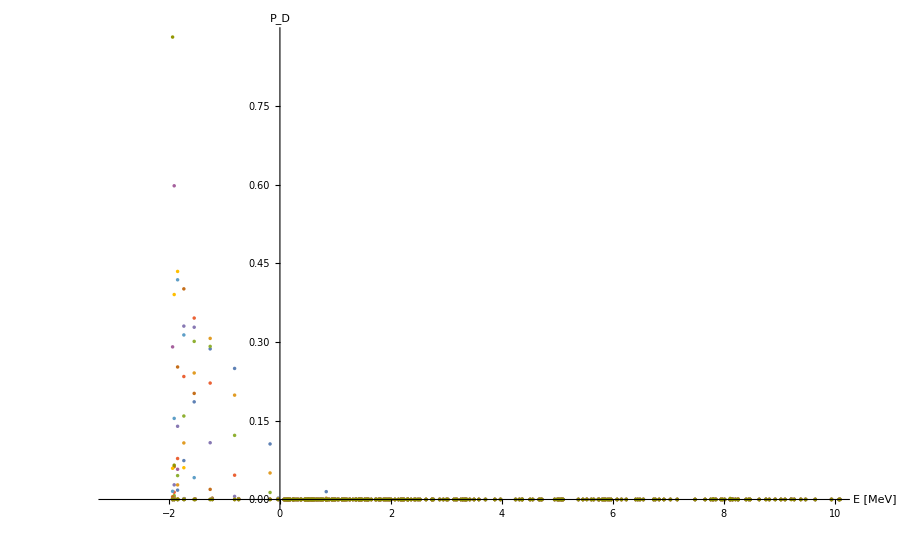

```mathematica
DaEn=Table[ciA[[a]].FSNormBare.esysFS[[eE]],{eE,FSbasisDim},{a,DAdim}];
maxEindex=FSbasisDim;
DaEsquare=Table[{esysFSp[[EE]][[1]],(DaEn[[EE]][[#]] DaEn[[EE]][[#]])},{EE,maxEindex}]&/@Range[DAdim];
SumADaE=Table[{esysFSp[[EE]][[1]],Total[Table[DaEn[[EE]][[aa]] DaEn[[EE]][[bb]],{aa,DAdim},{bb,DAdim}],2]},{EE,maxEindex}];
ListPlot[DaEsquare,AxesLabel->{"E [MeV]","P_D"},ImageSize->ImgSize,PlotRange->{{-3,10},All}]
```

```mathematica
nij=FSNormBare;
hij=FSHamBare;
aa=1;bb=1;

hab=ciAs[[aa]].hij.ciAs[[bb]]
nab=ciAs[[aa]].nij.ciAs[[bb]]
hab/nab
```

10.4167

1.47622

7.05629

“sanity” check:  what is ∑_(n=0)^(FS-dim) P_D(E^(n))=?
this is a treacherous sum as it brings us back to what reality P_D  is connected with.

```mathematica
Total[DaEsquare[[1]][[All,2]]]
```

1.